# Homework 1

## Knowles, John

## Problem 1.1

```mathematica
Tan[3 Pi/11]+4 Sin[2 Pi/11]
```

Cot[(5 π)/22]+4 Sin[(2 π)/11]

```mathematica
Simplify[Tan[3 Pi/11]+4 Sin[2 Pi/11]]
```

Cot[(5 π)/22]+4 Sin[(2 π)/11]

```mathematica
FullSimplify[Tan[3 Pi/11]+4 Sin[2 Pi/11]]
```

Cot[(5 π)/22]+4 Sin[(2 π)/11]

```mathematica
RootReduce[Cot[(5 π)/22]+4 Sin[(2 π)/11]]
```

√11

```mathematica
RootReduce[Tan[3Pi/11]+4Sin[2Pi/11]]
```

√11

## Exercise 1.1

```mathematica
(((64)^(1/3))*(2^2+((1/2)^2))-1)^(1/2)
```

4

```mathematica
Sqrt[CubeRoot[64](2^2+(1/2)^2)-1]
```

4

## Problem 1.2

```mathematica
4+6/4*3^−2+1
```

31/6

```mathematica
(*Certain Mathematica operators have higher precedence over other operations, therefore, in the simplest case, one can be certain that multiplication or division will be treated before addition or subtration.*)
```

## Problem 1.3

```mathematica
10^13-10^12
```

9000000000000

```mathematica
PrimePi[10^13]
```

346065536839

```mathematica
PrimePi[10^12]
```

37607912018

```mathematica
N[(346065536839-37607912018)/9000000000000]*100
```

3.42731

## Exercise 1.2

```mathematica
PrimeQ[123456789098765432111]
```

True

## Exercise 1.3

```mathematica
LCM[1,2,3,4,5]
```

60

```mathematica
2^(5-1)
```

16

```mathematica
LCM[1,2,3,4,5] > 2^(5-1)
```

True

## Exercise 1.4

```mathematica
32!
```

263130836933693530167218012160000000

```mathematica
IntegerExponent[32!]
```

7

## Problem 1.4

```mathematica
a = 98
```

98

```mathematica
b=75
```

75

```mathematica
c = a^a*b^b
```

588505020645437728536453591131463600799405243707437280561489034315907221008473769447232260519610491473752655063996301536290008346260850477235097238591277681036760705247800901438567482334220889060835026240781076012353878468275070190429687500000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
IntegerExponent[c]
```

98

```mathematica
Mod[c,10^98]
```

0

```mathematica
Mod[c,10^99]
```

500000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000

```mathematica
IntegerExponent[Mod[c,10^99]]
```

98

## Problem 1.5

```mathematica
Binomial[m+n, n] == (n+m)!/(n!m!)
```

Binomial[m+n,n]==((m+n)!)/(m! n!)

```mathematica
Binomial[m+n,n]==((m+n)!)/(m! n!)
```

Binomial[m+n,n]==((m+n)!)/(m! n!)

```mathematica
FullSimplify[Binomial[m+n, n] == (n+m)!/(n!m!)]
```

True

## Exercise 1.5

```mathematica
Factor[(1+x)^30+(1−x)^30]
```

2 (1+x^2) (1+14 x^2+x^4) (1+44 x^2+166 x^4+44 x^6+x^8) (1+376 x^2+4380 x^4+15944 x^6+24134 x^8+15944 x^10+4380 x^12+376 x^14+x^16)

## Exercise 1.6

```mathematica
Together[1/(1+x)+1/(1+1/(1+x))]
```

(3+3 x+x^2)/((1+x) (2+x))

```mathematica
Apart[1/(1+x)+1/(1+1/(1+x))]
```

1+1/(1+x)-1/(2+x)

## Problem 1.6

```mathematica
(Sin[x])^3(Cos[x])^3
```

Cos[x]^3 Sin[x]^3

```mathematica
Simplify[Sin[x]^3 Cos[x]^3==(3 Sin[2 x]-Sin[6 x])/32]
```

```mathematica
Simplify[(1+Sin[x]-Cos[x])/(1+Sin[x]+Cos[x])==Tan[x/2]]
```

True

## Exercise 1.7

```mathematica
mu1 = (1+Sin[x]-Cos[x])/(1+Sin[x]+Cos[x])
```

(1-Cos[x]+Sin[x])/(1+Cos[x]+Sin[x])

```mathematica
Simplify[ mu1]
```

Tan[x/2]

## Problem 1.7

```mathematica
Clear[x]
Expand[(1+x)^2]
```

1+2 x+x^2

## Problem 1.8

```mathematica
Manipulate[Factor[x^(2n)+x^n+1],{n, 1, 20, 1}]
```

## Problem 1.9

```mathematica
Manipulate[Sqrt[m^2 +n^2], {m, 1,100, 1},{n, 1, 13, 1}]
```

```mathematica
squareNumsQ[{n_Integer,m_Integer}]:=IntegerQ[Sqrt[m^2+n^2]]
```

```mathematica
allPairs=Flatten[Table[{m,n},{m,1,100},{n,1,13}],1];
```

```mathematica
squareNum = Select[allPairs,squareNumsQ]
```

{{3,4},{4,3},{5,12},{6,8},{8,6},{9,12},{12,5},{12,9},{15,8},{16,12},{24,7},{24,10},{35,12},{40,9},{60,11},{84,13}}

```mathematica
nonRepeated = Select[squareNum,OrderedQ]
```

{{3,4},{5,12},{6,8},{9,12}}

```mathematica
Length[nonRepeated]
```

4

## Problem 2.1

```mathematica
f[x_] := 1/(1+x)
```

```mathematica
f[f[f[f[x]]]]
```

1/(1+1/(1+1/(1+1/(1+x))))

```mathematica
Simplify[f[f[f[f[x]]]]]
```

(3+2 x)/(5+3 x)

## Exercise 2.1

```mathematica
f[x_]:=Sqrt[1+x]
```

```mathematica
f[f[f[f[f[x]]]]]
```

√(1+√(1+√(1+√(1+√(1+x)))))

## Problem 2.2

```mathematica
pQ [n_]:=PrimeQ[n!+1]
```

```mathematica
pQ[2]
```

True

```mathematica
pQ[5]
```

False

```mathematica
pQ[6]
```

False

```mathematica
pQ[3]
```

True

## Problem 2.3

```mathematica
B[z_]:=Binomial[z,1]+Binomial[z,2]+Binomial[z,3]+1
B[23]
```

2048

```mathematica
Mod[2^2008, B[23]]
```

0

## Exercise 2.2

```mathematica
Fibonacci[15]//Mod[#,5]&
```

0

```mathematica
PrimeQ[#!+1]&@4
```

False

```mathematica
18//2^#+#&
```

262162

```mathematica
(* Fibonacci[15] Inputs the 15th Fibonacci number in the nameless variable to which Mod[15,5] yields 0.
 PrimeQ determines whether or not the function evaluated at 4 is a prime number or not.
18 is the input for the nameless variable, which yields: 2^18+18, which yields 262162 *)
```

## Problem 3.1

```mathematica
Clear[a,b,c]
```

```mathematica
p={a,b,{c,d},e}
```

{a,b,{c,d},e}

```mathematica
{p[[1]],p[[2]],p[[3,1]],p[[3,2]],p[[4]]}
```

{a,b,c,d,e}

## Problem 3.2

```mathematica
Table[Fibonacci[i],{i,1,30}]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765,10946,17711,28657,46368,75025,121393,196418,317811,514229,832040}

## Problem 3.3

```mathematica
Table[Print[i," ",Factor[x^i+64]],{i,1,15}]
```

1 64+x

2 64+x^2

3 (4+x) (16-4 x+x^2)

4 (8-4 x+x^2) (8+4 x+x^2)

5 64+x^5

6 (4+x^2) (16-4 x^2+x^4)

7 64+x^7

8 (8-4 x^2+x^4) (8+4 x^2+x^4)

9 (4+x^3) (16-4 x^3+x^6)

10 64+x^10

11 64+x^11

12 (2-2 x+x^2) (2+2 x+x^2) (4-4 x+2 x^2-2 x^3+x^4) (4+4 x+2 x^2+2 x^3+x^4)

13 64+x^13

14 64+x^14

15 (4+x^5) (16-4 x^5+x^10)

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

## Problem 3.4

```mathematica
B[n_]:=1+Binomial[n,1]+Binomial[n,2]+Binomial[n,3]
```

```mathematica
Table[Mod[2^2008,B[n]],{n,3,50}]
```

{0,1,16,16,0,70,16,80,168,133,268,316,448,256,706,796,1096,723,1092,1030,0,256,458,1240,2704,2604,606,2922,640,1664,2704,4076,2824,1936,1024,8336,256,7882,6974,4192,4568,6061,1076,6896,704,16669,6856,16032}

## Problem 3.6

```mathematica
z = Table[n^2+n+41,{n,0,40}]
```

{41,43,47,53,61,71,83,97,113,131,151,173,197,223,251,281,313,347,383,421,461,503,547,593,641,691,743,797,853,911,971,1033,1097,1163,1231,1301,1373,1447,1523,1601,1681}

```mathematica
PrimeQ[z]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,False}

## Exercise 3.1

```mathematica
RandomInteger[3095,6]
```

{2290,1367,2141,272,505,805}

## Problem 3.7

```mathematica
primes = Table[3n^5+11,{n,1,2000}];
```

```mathematica
PrimeQ[primes];
```

```mathematica
z = Select[primes, PrimeQ];
```

```mathematica
Length[z]
```

97

## Problem 3.8

```mathematica
Length[Select[Table[Fibonacci[i],{i,1,500}], PrimeQ]]
```

18

## Exercise 3.2

```mathematica
z = Length[Select[Table[Fibonacci[i],{i,1,450}], EvenQ]]
```

150

```mathematica
y = Length[Select[Table[Fibonacci[i],{i,1,450}], OddQ]]
```

300

## Exercise 3.3

```mathematica
f[m_]:=(((m+3)^3)+1)/(3*m)
```

```mathematica
A = Select[Table[f[i],{i,1,499}], IntegerQ]
```

{21,117}

```mathematica
Table[f[i],{i,1,499}]//Select[IntegerQ]
```

{21,117}

## Problem 3.9

```mathematica
Select[Range[1000], PrimeQ[2^#+1 ] &]
```

{1,2,4,8,16}

## Exercise 3.4

```mathematica
Select[Range[0,20000],IntegerQ[(#^2+(#+1)^2)/1997] &]
```

{792,1204,2789,3201,4786,5198,6783,7195,8780,9192,10777,11189,12774,13186,14771,15183,16768,17180,18765,19177}

```mathematica
Select[Range[20000],Divisible[#^2+(#+1)^2,2009]&]
```

{}

## Exercise 3.5

```mathematica
n = Range[2,200];
```

```mathematica
z = (Factorial[#-1]+1&/@n)/n;
```

```mathematica
Length[Select[z,IntegerQ]]
```

46

## Problem 3.10

```mathematica
Clear[f]
```

```mathematica
f[n_]:=FromDigits[Reverse[IntegerDigits[n]]]
```

```mathematica
Select[Range[10000],f[#]^2==f[#^2]&]
```

{1,2,3,10,11,12,13,20,21,22,30,31,100,101,102,103,110,111,112,113,120,121,122,130,200,201,202,210,211,212,220,221,300,301,310,311,1000,1001,1002,1003,1010,1011,1012,1013,1020,1021,1022,1030,1031,1100,1101,1102,1103,1110,1111,1112,1113,1120,1121,1122,1130,1200,1201,1202,1210,1211,1212,1220,1300,1301,2000,2001,2002,2010,2011,2012,2020,2021,2022,2100,2101,2102,2110,2111,2120,2121,2200,2201,2202,2210,2211,3000,3001,3010,3011,3100,3101,3110,3111,10000}

```mathematica
Length[Out[85]]
```

100

## Problem 3.11

```mathematica
z = Select[Range[0,1000],OddQ[Binomial[1000,#]]&]
```

{0,8,32,40,64,72,96,104,128,136,160,168,192,200,224,232,256,264,288,296,320,328,352,360,384,392,416,424,448,456,480,488,512,520,544,552,576,584,608,616,640,648,672,680,704,712,736,744,768,776,800,808,832,840,864,872,896,904,928,936,960,968,992,1000}

```mathematica
Length[z]
```

64

```mathematica
FactorInteger[Length[z]]
```

{{2,6}}

## Exercise 3.6

```mathematica
a=Prime[Range[200]];
```

```mathematica
z=Mod[19^(#-1),(#^2)]==1&;
```

```mathematica
Select[a,z]
```

{3,7,13,43,137}

## Exercise 3.7

```mathematica
f[n_]:=FromDigits[Reverse[IntegerDigits[n]]]
```

```mathematica
Prime[700]
```

5279

```mathematica
Prime[660]
```

4937

```mathematica
Prime[670]
```

5003

```mathematica
a=Prime[Range[670]];
```

```mathematica
b = Select[a,PrimeQ[f[#]] &];
```

```mathematica
Length[b]
```

167

## Problem 3.12

```mathematica
Select[Range[10^5],Length[Divisors[#]]^4==# &]
```

{1,625,6561}

## Exercise 3.8

```mathematica
Select[Range[1000],IntegerQ[Sqrt[#!+(#+1)!]]&]
```

{4}

## Problem 3.13

```mathematica
Fibonacci[Range[20]]
```

{1,1,2,3,5,8,13,21,34,55,89,144,233,377,610,987,1597,2584,4181,6765}

```mathematica
Union[Last/@(IntegerDigits/@(Fibonacci/@Range[20]))]
```

{0,1,2,3,4,5,7,8,9}

## Problem 3.14

```mathematica
squareFreeQ[n_]:=Select[Last/@FactorInteger[n],#≠1&,1] =={}
```

```mathematica
squareFreeQ[2*6*4]
```

False

```mathematica
squareFreeQ[2*5*7]
```

True

## Exercise 3.9

```mathematica
Select[Range[10000],PrimeQ[#^6+1091]&,5]
```

{3906,4620,5166,5376,5460}

## Exercise 3.10

```mathematica
f[n_]:=Sort[IntegerDigits[n]]
```

```mathematica
c[n_]:=Length[Union[f/@(n Range[6])]]==1
```

```mathematica
Select[Range[100000,999999],c]
```

{142857}

## Problem 3.15

```mathematica
n=Range[30]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30}

```mathematica
Prime[2*n<# And#>n&]
```

Prime[2 n<#1 And #1>n&]

```mathematica
Length[Select[Range[#+1,2*#-1],PrimeQ]]& /@ Range[30]
```

{0,1,1,2,1,2,2,2,3,4,3,4,3,3,4,5,4,4,4,4,5,6,5,6,6,6,7,7,6,7}

## Problem 3.16

```mathematica
f[n_]:=n==StringReverse[n]
```

```mathematica
f["cat"]
```

False

```mathematica
f["illuminati"]
```

False

```mathematica
f["tacocat"]
```

True

```mathematica
Select[DictionaryLookup[],f]
```

{a,aha,aka,bib,bob,boob,bub,CFC,civic,dad,deed,deified,did,dud,DVD,eke,ere,eve,ewe,eye,gag,gig,huh,I,kayak,kook,level,ma'am,madam,mam,MGM,minim,mom,mum,nan,non,noon,nun,oho,pap,peep,pep,pip,poop,pop,pup,radar,redder,refer,repaper,reviver,rotor,sagas,sees,seres,sexes,shahs,sis,solos,SOS,stats,stets,tat,tenet,TNT,toot,tot,tut,wow,WWW}

```mathematica
DictionaryLookup[All]
```

{Arabic,BrazilianPortuguese,Breton,BritishEnglish,Catalan,Croatian,Danish,Dutch,English,Esperanto,Faroese,Finnish,French,Galician,German,Hebrew,Hindi,Hungarian,IrishGaelic,Italian,Latin,Polish,Portuguese,Russian,ScottishGaelic,Spanish,Swedish}

```mathematica
t = Table[{lang, Length[Select[DictionaryLookup[{lang, All}],f]]},{lang,DictionaryLookup[All]}]
```

{{Arabic,55},{BrazilianPortuguese,81},{Breton,57},{BritishEnglish,94},{Catalan,150},{Croatian,106},{Danish,156},{Dutch,83},{English,70},{Esperanto,14},{Faroese,85},{Finnish,72},{French,41},{Galician,92},{German,20},{Hebrew,159},{Hindi,27},{Hungarian,146},{IrishGaelic,42},{Italian,22},{Latin,21},{Polish,133},{Portuguese,121},{Russian,25},{ScottishGaelic,37},{Spanish,58},{Swedish,60}}

```mathematica
fnum = Last/@t
```

{55,81,57,94,150,106,156,83,70,14,85,72,41,92,20,159,27,146,42,22,21,133,121,25,37,58,60}

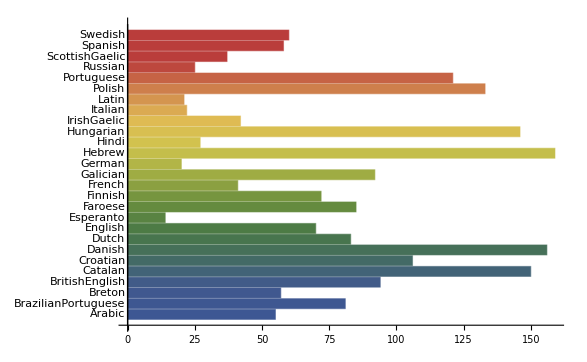

```mathematica
BarChart[fnum,BarOrigin->Left,ChartStyle->"DarkRainbow",ChartLabels->DictionaryLookup[All]]
```

## Problem 3.17

```mathematica
Short[Select[DictionaryLookup[],{StringReverse[#]}==DictionaryLookup[StringReverse[#]]&]]
```

{a,abut,agar,ah,«488»,yard,yaw,yaws,yob}

## Problem 48

```mathematica
a)
```

```mathematica
FullSimplify[ArcTan[2-Sqrt[3]]]
```

π/12

```mathematica
b)
```

```mathematica
Binomial[52,5]
```

2598960

```mathematica
c)
```

```mathematica
FullSimplify[Tan[ArcSin[x]]]
```

x/(√(1-x^2))

```mathematica
d)
```

```mathematica
E^(7*Log[3])
```

2187

## Problem 49

```mathematica
Clear[x]
```

```mathematica
Equal[Tan[x]+Sec[x]==Tan[x/2+Pi/4]]
```

True

```mathematica
FullSimplify[Tan[x]+Sec[x]==Tan[x/2+Pi/4]]
```

True

## Problem 50

### a)

```mathematica
121^2+121+1
```

14763

```mathematica
myList=#^2+#+1&[Range[121,1000]];
```

### b)

```mathematica
Part[myList,600]
```

519121

### c)

```mathematica
First[myList]
```

14763

```mathematica
Last[myList]
```

1001001

### d)

```mathematica
Take[myList,20]
```

{14763,15007,15253,15501,15751,16003,16257,16513,16771,17031,17293,17557,17823,18091,18361,18633,18907,19183,19461,19741}

```mathematica
Take[myList,-20]
```

{963343,965307,967273,969241,971211,973183,975157,977133,979111,981091,983073,985057,987043,989031,991021,993013,995007,997003,999001,1001001}

### e)

```mathematica
myPrimes = Select[myList,PrimeQ]
```

{17293,19183,20023,20593,21757,22651,23563,24181,26083,26407,27061,28057,28393,30103,31153,35533,35911,37057,37831,41413,42643,43891,46441,47743,53593,55933,60271,60763,71023,74257,77563,78121,82657,83233,84391,86143,95791,98911,108571,110557,113233,117307,118681,121453,123553,127807,136531,143263,145543,147073,154057,156421,158803,162007,163621,164431,171811,173473,181903,188791,189661,200257,205663,207481,208393,227053,239611,245521,250501,262657,268843,276151,281431,282493,284623,288907,292141,304153,307471,314161,320923,322057,327757,335821,339307,341641,364213,366631,371491,375157,386263,390001,392503,403861,412807,415381,446893,450913,459007,471283,485113,492103,519121,527803,530713,540961,552793,558757,570781,579883,581407,590593,598303,612307,617011,628057,637603,642403,660157,669943,671581,681451,684757,699733,704761,716563,731881,735307,740461,747361,766501,771763,792991,800131,805507,809101,830833,838141,843643,847321,860257,903451,920641,922561,939931,949651,963343,975157,981091,985057,987043}

### f)

```mathematica
Length[%]
```

151

### g)

```mathematica
Min[myPrimes]
```

17293

```mathematica
Max[myPrimes]
```

987043

## Problem 51

```mathematica
Prime[Range[1,20]]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
h[n_]:=Product[Prime[i],{i,1,n}]+1
```

```mathematica
myTable = Table[{h[n],Part[Part[FactorInteger[h[n]],1],1]>Prime[n],PrimeQ[h[n]]},{n,1,20}];
```

```mathematica
TableForm[Prepend[myTable,{"Product of Primes","Factorization Greater than Pn","isPrime?"}]]
```

Product of Primes | Factorization Greater than Pn | isPrime?
3 | True | True
7 | True | True
31 | True | True
211 | True | True
2311 | True | True
30031 | True | False
510511 | True | False
9699691 | True | False
223092871 | True | False
6469693231 | True | False
200560490131 | True | True
7420738134811 | True | False
304250263527211 | True | False
13082761331670031 | True | False
614889782588491411 | True | False
32589158477190044731 | True | False
1922760350154212639071 | True | False
117288381359406970983271 | True | False
7858321551080267055879091 | True | False
557940830126698960967415391 | True | False

## Problem 52

```mathematica
a)
```

```mathematica
2^60
```

1152921504606846976

```mathematica
IntegerDigits[2^60]
```

{1,1,5,2,9,2,1,5,0,4,6,0,6,8,4,6,9,7,6}

```mathematica
DigitSum[n_]:=Total[IntegerDigits[n]]
```

```mathematica
DigitSum[2^60]
```

82

```mathematica
b)
```

```mathematica
sumList=DigitSum/@Range[100]
```

{1,2,3,4,5,6,7,8,9,1,2,3,4,5,6,7,8,9,10,2,3,4,5,6,7,8,9,10,11,3,4,5,6,7,8,9,10,11,12,4,5,6,7,8,9,10,11,12,13,5,6,7,8,9,10,11,12,13,14,6,7,8,9,10,11,12,13,14,15,7,8,9,10,11,12,13,14,15,16,8,9,10,11,12,13,14,15,16,17,9,10,11,12,13,14,15,16,17,18,1}

## Problem 53

```mathematica
a)
```

```mathematica
(*A 3 digit number palindrome would have either the form 111, 222,...,999, or 121,232,...919 and so on. The first case yields 9 different cases while the second case will have distinct digits such that the number of possible palindromes would be 9*9+9+9+9 = 108 out of 999-99=900 possibilities. *)
```

```mathematica
N[108/900]
```

0.12

```mathematica
b)
```

```mathematica
A=RandomInteger[{100,999},100]
```

{197,406,197,831,765,843,856,470,590,194,398,494,318,662,257,646,973,866,146,890,239,547,472,538,171,282,279,757,555,290,215,538,302,515,686,350,214,696,147,349,451,497,602,287,385,917,928,243,909,527,760,785,130,906,579,463,866,701,512,863,375,236,196,810,871,692,964,972,679,840,674,555,572,455,747,345,160,573,151,981,528,810,656,448,668,867,494,368,603,239,770,329,864,126,785,529,968,226,536,876}

```mathematica
SameQ[#,IntegerReverse[#]]&/@A
```

{False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,True,True,False,True,True,False,False,False,False,True,True,False,False,True,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,True,False,False,False,True,False,False,False,True,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False}

```mathematica
freq = Length[Select[A,SameQ[#,IntegerReverse[#]]&]]
```

15

```mathematica
aP = N[freq/100,5]
```

0.15

```mathematica
c)
```

```mathematica
N[Abs[((.12-aP)/.12)]*100] (*percent error*)
```

25.

## Problem 54

```mathematica
a)
```

```mathematica
a=RandomInteger[100,1000];
```

```mathematica
A= (Fibonacci[#]^2+Fibonacci[#+1]^2)&[a];
```

```mathematica
B=Fibonacci[2*#+1]&[a];
```

```mathematica
SameQ[A ,B]
```

True

```mathematica
b)
```

```mathematica
b =Fibonacci[#]*Fibonacci[#+1]&[b];
```

```mathematica
c =Last/@IntegerDigits[c];
```

```mathematica
IntersectingQ[Union[c],Range[0,9]]
```

True

```mathematica
(*Since the union of ones digits from 1000 fibonacci numbers intersects with the range of numbers 0 through 9, we can see that the proposition that an integer existing between 0-9 never existing in the ones digit of a fibonacci number is false.*)
```

```mathematica
c)
```

```mathematica
e=RandomInteger[100]
```

66

```mathematica
A2=Sum[Fibonacci[2*i-1],{i,#}]&[e]
```

1725375039079340637797070384

```mathematica
B2=(Fibonacci[2*#]-1)&[e]
```

1725375039079340637797070383

```mathematica
SameQ[A2,B2]
```

False